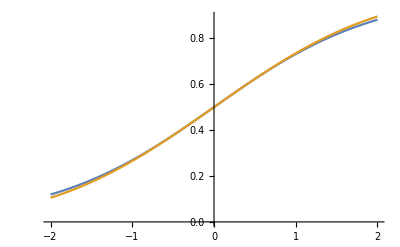

```mathematica
Plot[{LogisticSigmoid[x],1/2*(1+Erf[Sqrt[Pi]/4*x])},{x,-2,2}]
```

```mathematica
Manipulate[ss3=NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],m1'[t]==(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigman},m2'[t]==(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigman}},{m1,m2},{t,0,40}];
Plot[Evaluate[(m1[t]*1/Sqrt[2]+m2[t]*1/Sqrt[2])/Sqrt[m1[t]^2+m2[t]^2]/.ss3],{t,0,40}, PlotRange->{0.9,1}],{sigma,0,1}]
```

```mathematica
Manipulate[ss3=NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],m1'[t]==(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigma},m2'[t]==(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigma}},{m1,m2},{t,0,40}];
Plot[Evaluate[Sqrt[m1[t]^2+m2[t]^2]/.ss3],{t,0,40}],{sigma,0.00001,1}]
```

```mathematica
outsl = Table[{t0, (Evaluate[(m1[t]*1/Sqrt[2]+m2[t]*1/Sqrt[2])/Sqrt[m1[t]^2+m2[t]^2]/.ss3]/.t->t0)[[1]]},{t0,0.1,40,0.1}];
```

```mathematica
Export["outslsig1.csv",outsl,"CSV"]
```

outslsig1.csv

```mathematica
Manipulate[ss3=NDSolve[{m1[0]==0,m2[0]==1,m1'[t]==(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)*Pi/8]]-sigma1^2/Sqrt[2Pi](m1[t] Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2) Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma1^2->1+eps,sigma2^2->1-eps},m2'[t]==(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)*Pi/8]]-sigma2^2/Sqrt[2Pi](m2[t] Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)Pi/8)])/.{mu1->1,mu2->0,sigma1^2->1+eps,sigma2^2->1-eps}},{m1,m2},{t,0,40}];
Plot[Evaluate[m1[t]/Sqrt[m1[t]^2+m2[t]^2]/.ss3],{t,0,40}],{eps,-0.5,0.5}]
```

```mathematica
outslan= Table[{t0, (Evaluate[m1[t]/Sqrt[m1[t]^2+m2[t]^2]/.ss3]/.t->t0)[[1]]},{t0,0.1,40,0.1}];
```

```mathematica
Phi[x_]:=1/2+1/2*Erf[x/Sqrt[2]]
```

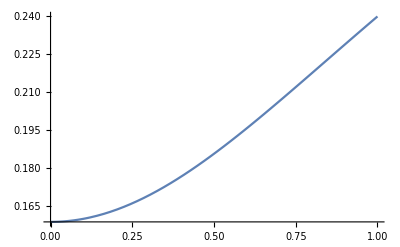

```mathematica
Plot[1-Phi[1/Sqrt[1+x^2]],{x,0,1}]
```

```mathematica
NIntegrate[((1-Phi[x1*w1*Sqrt[Pi/8]])*x1*PDF[NormalDistribution[mu1,sigma],x1]*PDF[NormalDistribution[mu2,sigma],x2])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],w1->1/Sqrt[3],sigma->0.1},{x1,-Infinity,Infinity},{x2,-Infinity,Infinity}]
```

0.280814

```mathematica
NIntegrate[((mu1-Phi[(sigma*u+mu1)*w1*Sqrt[Pi/8]]*(sigma*u+mu1))*PDF[NormalDistribution[0,1],u])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],w1->1/Sqrt[3],sigma->0.1},{u,-Infinity,Infinity}]
```

0.280814

```mathematica
(mu1-mu1*Phi[(mu1*w1*Sqrt[Pi/8])/Sqrt[1+w1^2*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](w1 sigma Sqrt[Pi/8])/Sqrt[1+w1^2sigma^2 Pi/8]*Exp[-1/2*(w1^2mu1^2Pi/8)/(1+w1^2sigma^2Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],w1->1/Sqrt[3],sigma->0.1}
```

0.280814

```mathematica
Series[(2/(mu1*m1[t]+mu2*m2[t])*(mu1*(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)*Pi/8]]-sigma1^2/Sqrt[2Pi](m1[t] Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) +mu2*(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-sigma2^2/Sqrt[2Pi](m2[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)])) - 2/(m1[t]^2+m2[t]^2)*(m1[t]*((mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-sigma1^2/Sqrt[2Pi](m1[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]))+m2[t]*((mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]]-sigma2^2/Sqrt[2Pi](m2[t]  Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2sigma2^2)Pi/8)]) )))/.{mu1->1,mu2->0, sigma2^2->1+eps, sigma1^2->1-eps},{eps,0,2}]
```

(m2[t]^2-Erf[(√(π/2) m1[t])/(√(8+π m1[t]^2+π m2[t]^2))] m2[t]^2)/(m1[t] (m1[t]^2+m2[t]^2))+(ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2+π m2[t]^2))) m2[t]^2 (256+56 π m1[t]^2+3 π^2 m1[t]^4+72 π m2[t]^2+8 π^2 m1[t]^2 m2[t]^2+5 π^2 m2[t]^4) eps)/(√2 (m1[t]^2+m2[t]^2) (8+π m1[t]^2+π m2[t]^2)^(5/2))-((ⅇ^(-(π m1[t]^2)/(2 (8+π m1[t]^2+π m2[t]^2))) π m2[t]^2 (m1[t]^2-m2[t]^2) (-4096-832 π m1[t]^2-24 π^2 m1[t]^4+2 π^3 m1[t]^6-1728 π m2[t]^2-248 π^2 m1[t]^2 m2[t]^2-5 π^3 m1[t]^4 m2[t]^2-240 π^2 m2[t]^4-18 π^3 m1[t]^2 m2[t]^4-11 π^3 m2[t]^6)) eps^2)/(4 (√2 (m1[t]^2+m2[t]^2) (8+π m1[t]^2+π m2[t]^2)^(9/2)))+O[eps]^3

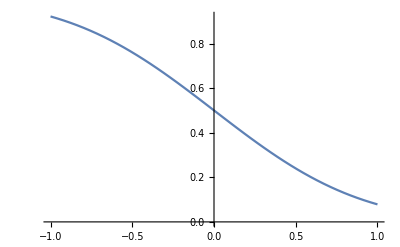

```mathematica
Plot[1-1/2*(1+Erf[x]),{x,-1,1}]
```

```mathematica
Plot[Phi'[x],{x,-10,10}]
```

-Graphics-

```mathematica
(16 m1[t]^2-16 mu1 m1[t]^2-mu1^2 π m1[t]^4+mu1^3 π m1[t]^4-mu2^2 π m1[t]^4+mu1 mu2 π m1[t]^3 m2[t]+mu1^2 mu2 π m1[t]^3 m2[t]-2 mu1^2 π m1[t]^2 m2[t]^2+mu1^3 π m1[t]^2 m2[t]^2-mu2^2 π m1[t]^2 m2[t]^2+mu1 mu2 π m1[t] m2[t]^3+mu1^2 mu2 π m1[t] m2[t]^3-mu1^2 π m2[t]^4)  /.{mu1->1/Sqrt[2.],mu2->1/Sqrt[2.]}//FullSimplify
```

-2.03087 m1[t]^4+2.68152 m1[t]^3 m2[t]+2.68152 m1[t] m2[t]^3-1.5708 m2[t]^4+m1[t]^2 (4.68629-3.60167 m2[t]^2)

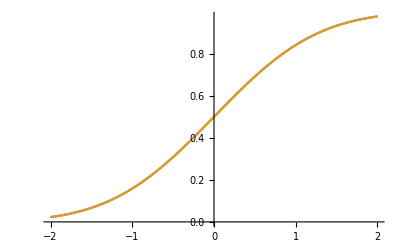

```mathematica
Plot[{Phi[x],-Phi[-x]+1},{x,-2,2}]
```

```mathematica
(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]) == Integrate[PDF[NormalDistribution[mu1,sigma],x1]*PDF[NormalDistribution[mu2,sigma],x2]*Phi[Sqrt[Pi/8](m1[t]*mu1+m2[t]*mu2)]*x1,{x1,-Infinity,Infinity},{x2,-Infinity,Infinity}]
```

```mathematica
NIntegrate[PDF[NormalDistribution[0,1],x1]*(Phi[Sqrt[Pi/8](m1[t]*(sigma*x1+mu1))])*(sigma*x1+mu1)/.{m1[t]->0.42,m2[t]->0.0,mu1->-3.42,mu2->1.22,sigma->0.2},{x1,-Infinity,Infinity}]
```

-0.6277

```mathematica
NIntegrate[((Phi[(sigma*u+mu1)*w1*Sqrt[Pi/8]]*(sigma*u+mu1))*PDF[NormalDistribution[0,1],u])/.{w1->0.42,m2[t]->0.0,mu1->-3.42,mu2->0,sigma->0.1},{u,-Infinity,Infinity},AccuracyGoal->80,WorkingPrecision->10]
```

-0.6289505254

```mathematica
NIntegrate[PDF[NormalDistribution[mu1,sigma],x1]*PDF[NormalDistribution[mu2,sigma],x2]*Phi[Sqrt[Pi/8](m1[t]*x1+m2[t]*x2)]*x1/.Thread[{m1[t],m2[t],mu1,mu2,sigma}->x],{x1,-Infinity,Infinity},{x2,-Infinity,Infinity},AccuracyGoal->80,WorkingPrecision->10]
```

0.004355551052

```mathematica
(mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]+sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)])/.Thread[{m1[t],m2[t],mu1,mu2,sigma}->x]
```

0.00438017

```mathematica
Thread[{m1[t],m2[t],mu1,mu2,sigma}->x]
```

{m1[t]→-1.5907,m2[t]→-1.11996,mu1→-2.07444,mu2→2.83012,sigma→-1.40534}

```mathematica
x=RandomReal[{-3,3},5]
```

{-2.60406,-0.528899,1.66714,0.522193,0.193345}

### Anisotropic

```mathematica
snrslan[eps_]:=(sslan = NDSolve[{m1[0]==0.0,m2[0]==1,m1'[t]==(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)*Pi/8]]-sigma1^2/Sqrt[2Pi](m1[t] Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2) Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)Pi/8)])/.{mu1->1,mu2->0,sigma1^2->1+eps,sigma2^2->1-eps},m2'[t]==(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)*Pi/8]]-sigma2^2/Sqrt[2Pi](m2[t] Sqrt[Pi/8])/Sqrt[1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2sigma1^2+m2[t]^2*sigma2^2)Pi/8)])/.{mu1->1,mu2->0,sigma1^2->1+eps,sigma2^2->1-eps}},{m1,m2},{t,0,40}];Table[{t0, (Evaluate[(m1[t])/Sqrt[m1[t]^2+m2[t]^2]/.sslan]/.t->t0)[[1]]},{t0,0.1,40,0.005}])
```

```mathematica
longtabslan = Table[{eps,snrslan[eps]},{eps,-0.5,0.5,0.01}]
```

{{-0.5,{{0.1,0.0506886},{0.105,0.0532559},{0.11,0.0558261},{0.115,0.0583991},{0.12,0.0609747},{0.125,0.063553},{0.13,0.066134},{0.135,0.0687174},{0.14,0.0713034},7963,{39.96,1.},{39.965,1.},{39.97,1.},{39.975,1.},{39.98,1.},{39.985,1.},{39.99,1.},{39.995,1.},{40.,1.}}},99,{0.5,1}}
 |  |  |  |

```mathematica
learntimesslan = Table[{el[[1]],Select[el[[2]], #[[2]]>0.8&,1]},{el,longtabslan}]
```

{{-0.5,{{1.955,0.800231}}},{-0.49,{{1.965,0.800534}}},{-0.48,{{1.975,0.800813}}},{-0.47,{{1.98,0.80012}}},{-0.46,{{1.99,0.800361}}},{-0.45,{{2.,0.800579}}},{-0.44,{{2.01,0.800773}}},{-0.43,{{2.015,0.800025}}},{-0.42,{{2.025,0.800182}}},{-0.41,{{2.035,0.800316}}},{-0.4,{{2.045,0.800428}}},{-0.39,{{2.055,0.800517}}},{-0.38,{{2.065,0.800584}}},{-0.37,{{2.075,0.800629}}},{-0.36,{{2.085,0.800652}}},{-0.35,{{2.095,0.800653}}},{-0.34,{{2.105,0.800631}}},{-0.33,{{2.115,0.800589}}},{-0.32,{{2.125,0.800524}}},{-0.31,{{2.135,0.800438}}},{-0.3,{{2.145,0.80033}}},{-0.29,{{2.155,0.8002}}},{-0.28,{{2.165,0.80005}}},{-0.27,{{2.18,0.800685}}},{-0.26,{{2.19,0.800485}}},{-0.25,{{2.2,0.800264}}},{-0.24,{{2.21,0.800022}}},{-0.23,{{2.225,0.800538}}},{-0.22,{{2.235,0.800248}}},{-0.21,{{2.25,0.800702}}},{-0.2,{{2.26,0.800364}}},{-0.19,{{2.27,0.800005}}},{-0.18,{{2.285,0.80037}}},{-0.17,{{2.3,0.800701}}},{-0.16,{{2.31,0.800269}}},{-0.15,{{2.325,0.800539}}},{-0.14,{{2.335,0.80006}}},{-0.13,{{2.35,0.80027}}},{-0.12,{{2.365,0.800447}}},{-0.11,{{2.38,0.80059}}},{-0.1,{{2.39,0.800014}}},{-0.09,{{2.405,0.800099}}},{-0.08,{{2.42,0.800151}}},{-0.07,{{2.435,0.80017}}},{-0.06,{{2.45,0.800158}}},{-0.05,{{2.465,0.800113}}},{-0.04,{{2.48,0.800036}}},{-0.03,{{2.5,0.800566}}},{-0.02,{{2.515,0.800419}}},{-0.01,{{2.53,0.800241}}},{0.,{{2.545,0.800031}}},{0.01,{{2.565,0.800401}}},{0.02,{{2.58,0.800123}}},{0.03,{{2.6,0.800411}}},{0.04,{{2.615,0.800065}}},{0.05,{{2.635,0.800272}}},{0.06,{{2.655,0.800436}}},{0.07,{{2.675,0.800555}}},{0.08,{{2.69,0.80007}}},{0.09,{{2.71,0.800111}}},{0.1,{{2.73,0.800109}}},{0.11,{{2.75,0.800065}}},{0.12,{{2.775,0.800513}}},{0.13,{{2.795,0.800379}}},{0.14,{{2.815,0.800203}}},{0.15,{{2.84,0.800499}}},{0.16,{{2.86,0.800234}}},{0.17,{{2.885,0.800429}}},{0.18,{{2.905,0.800077}}},{0.19,{{2.93,0.800171}}},{0.2,{{2.955,0.800213}}},{0.21,{{2.98,0.800201}}},{0.22,{{3.005,0.800138}}},{0.23,{{3.03,0.800022}}},{0.24,{{3.06,0.800308}}},{0.25,{{3.085,0.800083}}},{0.26,{{3.115,0.800246}}},{0.27,{{3.145,0.800346}}},{0.28,{{3.175,0.800383}}},{0.29,{{3.205,0.800357}}},{0.3,{{3.235,0.800269}}},{0.31,{{3.265,0.80012}}},{0.32,{{3.3,0.800307}}},{0.33,{{3.33,0.80003}}},{0.34,{{3.365,0.800077}}},{0.35,{{3.4,0.800052}}},{0.36,{{3.44,0.800325}}},{0.37,{{3.475,0.80015}}},{0.38,{{3.515,0.800262}}},{0.39,{{3.555,0.800291}}},{0.4,{{3.595,0.800238}}},{0.41,{{3.635,0.800103}}},{0.42,{{3.68,0.800218}}},{0.43,{{3.725,0.800241}}},{0.44,{{3.77,0.800172}}},{0.45,{{3.815,0.800012}}},{0.46,{{3.865,0.800066}}},{0.47,{{3.915,0.800018}}},{0.48,{{3.97,0.800159}}},{0.49,{{4.025,0.800188}}},{0.5,{{4.08,0.800106}}}}

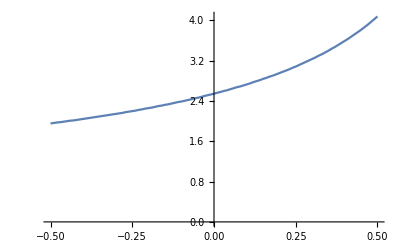

```mathematica
ListLinePlot[Table[{el[[1]],el[[2,1,1]]},{el,learntimesslan}]]
```

```mathematica
Export["outslanlearntimes.csv",Table[{el[[1]],el[[2,1,1]]},{el,learntimesslan}],"CSV"]
```

### Isotropic

```mathematica
snrsl[sig_]:=(ssl = NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],m1'[t]==(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sig},m2'[t]==(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sig}},{m1,m2},{t,0,40}];Table[{t0, (Evaluate[(m1[t]*1/Sqrt[2]+m2[t]*1/Sqrt[2])/Sqrt[m1[t]^2+m2[t]^2]/.ssl]/.t->t0)[[1]]},{t0,0.1,40,0.005}])
```

```mathematica
longtabsl = Table[{sig,snrsl[sig]},{sig,0.01,1.01,0.01}]
```

{1}
 |  |  |  |

```mathematica
learntimessl = Table[{el[[1]],Select[el[[2]], #[[2]]>0.8&,1]},{el,longtabsl}]
```

{{0.01,{{4.17,0.800042}}},{0.02,{{4.17,0.800101}}},{0.03,{{4.17,0.8002}}},{0.04,{{4.165,0.80012}}},{0.05,{{4.16,0.800079}}},{0.06,{{4.155,0.800076}}},{0.07,{{4.15,0.800112}}},{0.08,{{4.145,0.800185}}},{0.09,{{4.135,0.800074}}},{0.1,{{4.13,0.800221}}},{0.11,{{4.12,0.800181}}},{0.12,{{4.11,0.800176}}},{0.13,{{4.1,0.800205}}},{0.14,{{4.085,0.800039}}},{0.15,{{4.075,0.800132}}},{0.16,{{4.06,0.800026}}},{0.17,{{4.05,0.800183}}},{0.18,{{4.035,0.800135}}},{0.19,{{4.02,0.800114}}},{0.2,{{4.005,0.80012}}},{0.21,{{3.99,0.800151}}},{0.22,{{3.975,0.800208}}},{0.23,{{3.955,0.800042}}},{0.24,{{3.94,0.800143}}},{0.25,{{3.92,0.800016}}},{0.26,{{3.905,0.80016}}},{0.27,{{3.885,0.800069}}},{0.28,{{3.87,0.800252}}},{0.29,{{3.85,0.800193}}},{0.3,{{3.83,0.800147}}},{0.31,{{3.81,0.800114}}},{0.32,{{3.79,0.800092}}},{0.33,{{3.77,0.800082}}},{0.34,{{3.75,0.800081}}},{0.35,{{3.73,0.800089}}},{0.36,{{3.71,0.800106}}},{0.37,{{3.69,0.80013}}},{0.38,{{3.67,0.80016}}},{0.39,{{3.65,0.800197}}},{0.4,{{3.63,0.800238}}},{0.41,{{3.61,0.800284}}},{0.42,{{3.585,0.800026}}},{0.43,{{3.565,0.800074}}},{0.44,{{3.545,0.800124}}},{0.45,{{3.525,0.800175}}},{0.46,{{3.505,0.800227}}},{0.47,{{3.485,0.800277}}},{0.48,{{3.465,0.800327}}},{0.49,{{3.44,0.800039}}},{0.5,{{3.42,0.80008}}},{0.51,{{3.4,0.800117}}},{0.52,{{3.38,0.800151}}},{0.53,{{3.36,0.800179}}},{0.54,{{3.34,0.800202}}},{0.55,{{3.32,0.800219}}},{0.56,{{3.3,0.800229}}},{0.57,{{3.28,0.800232}}},{0.58,{{3.26,0.800226}}},{0.59,{{3.24,0.800212}}},{0.6,{{3.22,0.800188}}},{0.61,{{3.2,0.800153}}},{0.62,{{3.18,0.800108}}},{0.63,{{3.16,0.800052}}},{0.64,{{3.145,0.80039}}},{0.65,{{3.125,0.800314}}},{0.66,{{3.105,0.800224}}},{0.67,{{3.085,0.800121}}},{0.68,{{3.065,0.800003}}},{0.69,{{3.05,0.800303}}},{0.7,{{3.03,0.80016}}},{0.71,{{3.01,0.8}}},{0.72,{{2.995,0.800273}}},{0.73,{{2.975,0.800085}}},{0.74,{{2.96,0.800338}}},{0.75,{{2.94,0.80012}}},{0.76,{{2.925,0.800352}}},{0.77,{{2.905,0.800101}}},{0.78,{{2.89,0.800311}}},{0.79,{{2.87,0.800024}}},{0.8,{{2.855,0.80021}}},{0.81,{{2.84,0.800385}}},{0.82,{{2.82,0.800045}}},{0.83,{{2.805,0.800193}}},{0.84,{{2.79,0.80033}}},{0.85,{{2.775,0.800455}}},{0.86,{{2.755,0.800039}}},{0.87,{{2.74,0.800133}}},{0.88,{{2.725,0.800215}}},{0.89,{{2.71,0.800283}}},{0.9,{{2.695,0.800337}}},{0.91,{{2.68,0.800376}}},{0.92,{{2.665,0.800402}}},{0.93,{{2.65,0.800412}}},{0.94,{{2.635,0.800407}}},{0.95,{{2.62,0.800386}}},{0.96,{{2.605,0.800349}}},{0.97,{{2.59,0.800295}}},{0.98,{{2.575,0.800225}}},{0.99,{{2.56,0.800137}}},{1.,{{2.545,0.800031}}},{1.01,{{2.535,0.800532}}}}

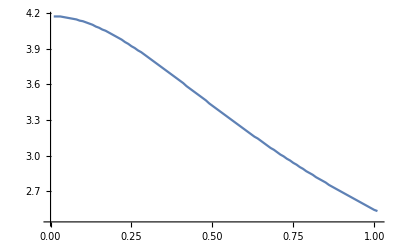

```mathematica
ListLinePlot[Table[{el[[1]],el[[2,1,1]]},{el,learntimessl}]]
```

```mathematica
Export["outsllearntimes.csv",Table[{el[[1]],el[[2,1,1]]},{el,learntimessl}],"CSV"]
```

outsllearntimes.csv

### Covariance

```mathematica
covterms1[t] = (C11[t]D[(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t],m1[t]]+
2C12[t]*D[(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t],m2[t]]+
C22[t]D[(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m2[t],m2[t]])//FullSimplify
```

1/(√2 (8+π sigma^2 (m1[t]^2+m2[t]^2))^(9/2))ⅇ^(-(π (mu1 m1[t]+mu2 m2[t])^2)/(2 (8+π sigma^2 (m1[t]^2+m2[t]^2)))) π (C22[t] ((mu2^2+sigma^2) m1[t] (8+π sigma^2 m1[t]^2)^2 (8 (mu1^2+sigma^2)+π sigma^4 m1[t]^2)-mu1 mu2 (8+π sigma^2 m1[t]^2) (-64 (mu2^2+3 sigma^2)+16 π sigma^2 (mu1^2+sigma^2) m1[t]^2+π^2 sigma^4 (mu2^2+5 sigma^2) m1[t]^4) m2[t]-π sigma^2 m1[t] (64 mu2^2 (mu1^2+mu2^2+4 sigma^2)-8 π sigma^2 (mu1^4+2 mu1^2 (mu2^2+2 sigma^2)-2 (mu2^4+4 mu2^2 sigma^2)) m1[t]^2+π^2 sigma^4 (mu2^4+4 mu2^2 sigma^2-mu1^2 (3 mu2^2+4 sigma^2)) m1[t]^4) m2[t]^2+mu1 mu2 π sigma^2 (64 (mu2^2+6 sigma^2)+π sigma^2 m1[t]^2 (-8 mu1^2+32 (mu2^2+2 sigma^2)+π sigma^2 (-3 mu1^2+3 mu2^2+2 sigma^2) m1[t]^2)) m2[t]^3-π^2 sigma^4 m1[t] (8 (5 mu2^2 sigma^2+3 sigma^4+mu1^2 (2 mu2^2+3 sigma^2))+π sigma^2 (-mu1^4+5 mu2^2 sigma^2+3 sigma^4+mu1^2 (3 mu2^2-2 sigma^2)) m1[t]^2) m2[t]^4+mu1 mu2 π^2 sigma^6 (24+π (mu1^2+7 sigma^2) m1[t]^2) m2[t]^5-2 π^3 sigma^8 (mu1^2+sigma^2) m1[t] m2[t]^6)+C11[t] (mu1 mu2 (mu1^2+3 sigma^2) m2[t] (8+π sigma^2 m2[t]^2)^3+3 π^2 sigma^8 m1[t]^5 (8+π (mu2^2+sigma^2) m2[t]^2)-3 mu1 mu2 π sigma^2 m1[t]^2 m2[t] (8+π sigma^2 m2[t]^2) (8 (mu1^2+2 sigma^2)+π sigma^2 (mu1^2-mu2^2+2 sigma^2) m2[t]^2)-mu1 mu2 π^2 sigma^6 m1[t]^4 m2[t] (72+π (mu2^2+9 sigma^2) m2[t]^2)+m1[t] (8+π sigma^2 m2[t]^2)^2 (8 (mu1^4+6 mu1^2 sigma^2+3 sigma^4)+π sigma^2 (mu1^4-3 mu1^2 mu2^2+6 mu1^2 sigma^2-3 mu2^2 sigma^2+3 sigma^4) m2[t]^2)+π sigma^4 m1[t]^3 (384 (mu1^2+sigma^2)+24 π (4 sigma^4+mu1^2 (mu2^2+4 sigma^2)) m2[t]^2+π^2 sigma^2 (-mu2^4+6 sigma^4+3 mu1^2 (mu2^2+2 sigma^2)) m2[t]^4))+2 C12[t] (-2 π^3 sigma^8 (mu2^2+sigma^2) m1[t]^6 m2[t]+(mu1^2+sigma^2) m2[t] (8+π sigma^2 m2[t]^2)^2 (8 (mu2^2+sigma^2)+π sigma^4 m2[t]^2)+mu1 mu2 π^2 sigma^6 m1[t]^5 (24+π (mu2^2+7 sigma^2) m2[t]^2)+π^2 sigma^4 m1[t]^4 m2[t] (-8 (3 sigma^2 (mu2^2+sigma^2)+mu1^2 (2 mu2^2+5 sigma^2))+π sigma^2 (mu2^4+2 mu2^2 sigma^2-3 sigma^4-mu1^2 (3 mu2^2+5 sigma^2)) m2[t]^2)+mu1 mu2 π sigma^2 m1[t]^3 (64 (mu1^2+6 sigma^2)+8 π sigma^2 (4 mu1^2-mu2^2+8 sigma^2) m2[t]^2+π^2 sigma^4 (3 mu1^2-3 mu2^2+2 sigma^2) m2[t]^4)-mu1 mu2 m1[t] (8+π sigma^2 m2[t]^2) (-64 (mu1^2+3 sigma^2)+16 π sigma^2 (mu2^2+sigma^2) m2[t]^2+π^2 sigma^4 (mu1^2+5 sigma^2) m2[t]^4)+π sigma^2 m1[t]^2 m2[t] (-64 mu1^2 (mu1^2+mu2^2+4 sigma^2)+8 π sigma^2 (-2 mu1^4+mu2^4+4 mu2^2 sigma^2+2 mu1^2 (mu2^2-4 sigma^2)) m2[t]^2-π^2 sigma^4 (mu1^4-4 mu2^2 sigma^2+mu1^2 (-3 mu2^2+4 sigma^2)) m2[t]^4)))

```mathematica
covterms2[t] = (C11[t]D[(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t],m1[t]]+
2C12[t]*D[(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t],m2[t]]+
C22[t]D[(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m2[t],m2[t]])//FullSimplify
```

1/(√2 (8+π sigma^2 (m1[t]^2+m2[t]^2))^(9/2))ⅇ^(-(π (mu1 m1[t]+mu2 m2[t])^2)/(2 (8+π sigma^2 (m1[t]^2+m2[t]^2)))) π (C22[t] (mu1 mu2 (mu2^2+3 sigma^2) m1[t] (8+π sigma^2 m1[t]^2)^3+(8+π sigma^2 m1[t]^2)^2 (8 (mu2^4+6 mu2^2 sigma^2+3 sigma^4)+π sigma^2 (mu2^4+6 mu2^2 sigma^2+3 sigma^4-3 mu1^2 (mu2^2+sigma^2)) m1[t]^2) m2[t]-3 mu1 mu2 π sigma^2 m1[t] (8+π sigma^2 m1[t]^2) (8 (mu2^2+2 sigma^2)+π sigma^2 (-mu1^2+mu2^2+2 sigma^2) m1[t]^2) m2[t]^2+π sigma^4 (384 (mu2^2+sigma^2)+24 π (mu1^2 mu2^2+4 sigma^2 (mu2^2+sigma^2)) m1[t]^2+π^2 sigma^2 (-mu1^4+3 mu1^2 mu2^2+6 sigma^2 (mu2^2+sigma^2)) m1[t]^4) m2[t]^3-mu1 mu2 π^2 sigma^6 m1[t] (72+π (mu1^2+9 sigma^2) m1[t]^2) m2[t]^4+3 π^2 sigma^8 (8+π (mu1^2+sigma^2) m1[t]^2) m2[t]^5)+2 C12[t] ((mu2^2+sigma^2) m1[t] (8+π sigma^2 m1[t]^2)^2 (8 (mu1^2+sigma^2)+π sigma^4 m1[t]^2)-mu1 mu2 (8+π sigma^2 m1[t]^2) (-64 (mu2^2+3 sigma^2)+16 π sigma^2 (mu1^2+sigma^2) m1[t]^2+π^2 sigma^4 (mu2^2+5 sigma^2) m1[t]^4) m2[t]-π sigma^2 m1[t] (64 mu2^2 (mu1^2+mu2^2+4 sigma^2)-8 π sigma^2 (mu1^4+2 mu1^2 (mu2^2+2 sigma^2)-2 (mu2^4+4 mu2^2 sigma^2)) m1[t]^2+π^2 sigma^4 (mu2^4+4 mu2^2 sigma^2-mu1^2 (3 mu2^2+4 sigma^2)) m1[t]^4) m2[t]^2+mu1 mu2 π sigma^2 (64 (mu2^2+6 sigma^2)+π sigma^2 m1[t]^2 (-8 mu1^2+32 (mu2^2+2 sigma^2)+π sigma^2 (-3 mu1^2+3 mu2^2+2 sigma^2) m1[t]^2)) m2[t]^3-π^2 sigma^4 m1[t] (8 (5 mu2^2 sigma^2+3 sigma^4+mu1^2 (2 mu2^2+3 sigma^2))+π sigma^2 (-mu1^4+5 mu2^2 sigma^2+3 sigma^4+mu1^2 (3 mu2^2-2 sigma^2)) m1[t]^2) m2[t]^4+mu1 mu2 π^2 sigma^6 (24+π (mu1^2+7 sigma^2) m1[t]^2) m2[t]^5-2 π^3 sigma^8 (mu1^2+sigma^2) m1[t] m2[t]^6)+C11[t] (-2 π^3 sigma^8 (mu2^2+sigma^2) m1[t]^6 m2[t]+(mu1^2+sigma^2) m2[t] (8+π sigma^2 m2[t]^2)^2 (8 (mu2^2+sigma^2)+π sigma^4 m2[t]^2)+mu1 mu2 π^2 sigma^6 m1[t]^5 (24+π (mu2^2+7 sigma^2) m2[t]^2)+π^2 sigma^4 m1[t]^4 m2[t] (-8 (3 sigma^2 (mu2^2+sigma^2)+mu1^2 (2 mu2^2+5 sigma^2))+π sigma^2 (mu2^4+2 mu2^2 sigma^2-3 sigma^4-mu1^2 (3 mu2^2+5 sigma^2)) m2[t]^2)+mu1 mu2 π sigma^2 m1[t]^3 (64 (mu1^2+6 sigma^2)+8 π sigma^2 (4 mu1^2-mu2^2+8 sigma^2) m2[t]^2+π^2 sigma^4 (3 mu1^2-3 mu2^2+2 sigma^2) m2[t]^4)-mu1 mu2 m1[t] (8+π sigma^2 m2[t]^2) (-64 (mu1^2+3 sigma^2)+16 π sigma^2 (mu2^2+sigma^2) m2[t]^2+π^2 sigma^4 (mu1^2+5 sigma^2) m2[t]^4)+π sigma^2 m1[t]^2 m2[t] (-64 mu1^2 (mu1^2+mu2^2+4 sigma^2)+8 π sigma^2 (-2 mu1^4+mu2^4+4 mu2^2 sigma^2+2 mu1^2 (mu2^2-4 sigma^2)) m2[t]^2-π^2 sigma^4 (mu1^4-4 mu2^2 sigma^2+mu1^2 (-3 mu2^2+4 sigma^2)) m2[t]^4)))

```mathematica
covap11[t]=(2*C11[t]*D[(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t]]+2*C12[t]*D[(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m2[t]])//FullSimplify
```

1/((8+π sigma^2 (m1[t]^2+m2[t]^2))^(5/2))√2 ⅇ^(-(π (mu1 m1[t]+mu2 m2[t])^2)/(2 (8+π sigma^2 (m1[t]^2+m2[t]^2)))) (-64 ((mu1^2+sigma^2) C11[t]+mu1 mu2 C12[t])+π^2 sigma^4 m2[t] (C12[t] m1[t]-C11[t] m2[t]) ((mu2^2+sigma^2) m1[t]^2-2 mu1 mu2 m1[t] m2[t]+(mu1^2+sigma^2) m2[t]^2)+8 π sigma^2 (-((sigma^2 C11[t]+mu1 mu2 C12[t]) m1[t]^2)+(2 mu1 mu2 C11[t]+(mu1^2+mu2^2+sigma^2) C12[t]) m1[t] m2[t]-(2 (mu1^2+sigma^2) C11[t]+mu1 mu2 C12[t]) m2[t]^2))

```mathematica
covap12[t]=(C11[t]*D[(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t]]+C12[t]*D[(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t]]+C12[t]*D[(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m2[t]]+C22[t]*D[(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m2[t]])//FullSimplify
```

1/(√2 (8+π sigma^2 (m1[t]^2+m2[t]^2))^(5/2))ⅇ^(-(π (mu1 m1[t]+mu2 m2[t])^2)/(2 (8+π sigma^2 (m1[t]^2+m2[t]^2)))) (C22[t] (-64 mu1 mu2+π sigma^2 (-8 mu1 mu2 m1[t]^2+m1[t] (8 (mu1^2+mu2^2+sigma^2)+π sigma^2 (mu2^2+sigma^2) m1[t]^2) m2[t]-2 mu1 mu2 (4+π sigma^2 m1[t]^2) m2[t]^2+π sigma^2 (mu1^2+sigma^2) m1[t] m2[t]^3))+C12[t] (-64 (mu1^2+mu2^2+2 sigma^2)+π sigma^2 (-8 (2 mu2^2+3 sigma^2) m1[t]^2-π sigma^2 (mu2^2+sigma^2) m1[t]^4+2 mu1 mu2 m1[t] (16+π sigma^2 m1[t]^2) m2[t]-(8 (2 mu1^2+3 sigma^2)+π sigma^2 (mu1^2+mu2^2+2 sigma^2) m1[t]^2) m2[t]^2+2 mu1 mu2 π sigma^2 m1[t] m2[t]^3-π sigma^2 (mu1^2+sigma^2) m2[t]^4))+C11[t] (-64 mu1 mu2+π sigma^2 (π sigma^2 (mu2^2+sigma^2) m1[t]^3 m2[t]-8 mu1 mu2 m2[t]^2-2 mu1 mu2 m1[t]^2 (4+π sigma^2 m2[t]^2)+m1[t] m2[t] (8 (mu1^2+mu2^2+sigma^2)+π sigma^2 (mu1^2+sigma^2) m2[t]^2))))

```mathematica
covap22[t]=(2*C12[t]*D[(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m1[t]]+2*C22[t]*D[(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]),m2[t]])//FullSimplify
```

1/((8+π sigma^2 (m1[t]^2+m2[t]^2))^(5/2))√2 ⅇ^(-(π (mu1 m1[t]+mu2 m2[t])^2)/(2 (8+π sigma^2 (m1[t]^2+m2[t]^2)))) (-64 (mu1 mu2 C12[t]+(mu2^2+sigma^2) C22[t])-π^2 sigma^4 m1[t] (C22[t] m1[t]-C12[t] m2[t]) ((mu2^2+sigma^2) m1[t]^2-2 mu1 mu2 m1[t] m2[t]+(mu1^2+sigma^2) m2[t]^2)+8 π sigma^2 (-((mu1 mu2 C12[t]+2 (mu2^2+sigma^2) C22[t]) m1[t]^2)+((mu1^2+mu2^2+sigma^2) C12[t]+2 mu1 mu2 C22[t]) m1[t] m2[t]-(mu1 mu2 C12[t]+sigma^2 C22[t]) m2[t]^2))

```mathematica
solcovar2=Table[NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],C11[0]==0.1,C12[0]==0,C22[0]==0.1,m1'[t]==(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]+covterms1[t]-0.1m1[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},m2'[t]==(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]+covterms2[t]-0.1m2[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C11'[t]==(covap11[t]-2C11[t]*0.1)/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C12'[t]==(covap12[t]-2C12[t]*0.1)/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C22'[t]==(covap22[t]-2C22[t]*0.1)/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval}},{m1,m2,C11,C12,C22},{t,0,40}],{sigval,{1,0.5,  0.0}}];
```

```mathematica
Manipulate[solcovar=NDSolve[{m1[0]==1/Sqrt[2],m2[0]==-1/Sqrt[2],C11[0]==0.1,C12[0]==0,C22[0]==0.1,m1'[t]==(mu1-mu1*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m1[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]+covterms1[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},m2'[t]==(mu2-mu2*Phi[((mu1*m1[t]+mu2*m2[t])*Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)*sigma^2*Pi/8]]-sigma/Sqrt[2Pi](m2[t] sigma Sqrt[Pi/8])/Sqrt[1+(m1[t]^2+m2[t]^2)sigma^2 Pi/8]*Exp[-1/2*((m1[t]mu1+m2[t]mu2)^2Pi/8)/(1+(m1[t]^2+m2[t]^2)sigma^2Pi/8)]+covterms2[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C11'[t]==(covap11[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C12'[t]==(covap12[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval},C22'[t]==(covap22[t])/.{mu1->1/Sqrt[2],mu2->1/Sqrt[2],sigma->sigval}},{m1,m2,C11,C12,C22},{t,0,500}];
Plot[Evaluate[(C11[t]+C22[t])/.solcovar],{t,0,500}],{sigval,0,1}]
```

```mathematica
Export["outcovtraceslsig10.csv",Table[{tval,(Evaluate[(C11[t]+C22[t])/.solcovar2[[1]]]/.t->tval)[[1]]},{tval,0,40,0.1}],"CSV"]
Export["outcovtraceslsig05.csv",Table[{tval,(Evaluate[(C11[t]+C22[t])/.solcovar2[[2]]]/.t->tval)[[1]]},{tval,0,40,0.1}],"CSV"]
Export["outcovtraceslsig00.csv",Table[{tval,(Evaluate[(C11[t]+C22[t])/.solcovar2[[3]]]/.t->tval)[[1]]},{tval,0,40,0.1}],"CSV"]
```

outcovtraceslsig10.csv

outcovtraceslsig05.csv

outcovtraceslsig00.csv